```mathematica
FromVoigtToCart[sig_]:={{sig[[1]],sig[[6]],sig[[4]]},{sig[[6]],sig[[2]],sig[[5]]},{sig[[4]],sig[[5]],sig[[3]]}}
FromCartToVoigt[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],sig[[1,3]],sig[[2,3]],sig[[1,2]]}
FromCartToVoigt2[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],2sig[[1,3]],2sig[[2,3]],2sig[[1,2]]}
P=1/3{{2,-1,-1,0,0,0},{-1,2,-1,0,0,0},{-1,-1,2,0,0,0},{0,0,0,6,0,0},{0,0,0,0,6,0},{0,0,0,0,0,6}};
dadsigmax[sigma_]:=P Sqrt[3]/(2 Sqrt[J2[sigma]])-Sqrt[3]/(4 J2[sigma]^(3/2))Outer[Times,S[sigma],S[sigma]]
Elast[K_,G_]:={{(4 G)/3+K,-(2 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,(4 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,-(2 G)/3+K,(4 G)/3+K,0,0,0},{0,0,0,G,0,0},{0,0,0,0,G,0},{0,0,0,0,0,G}};
(*S[{sxx_,syy_,szz_,sxz_,syz_,sxy_}]:=Block[{sigcart,scart},
sigcart={{sxx,sxy,sxz},{sxy,syy,syz},{sxz,syz,szz}};
scart=sigcart-1/3 Tr[sigcart]IdentityMatrix[3];
FromCartToVoigt[scart]
];
J2[{sxx_,syy_,szz_,sxz_,syz_,sxy_}]:=Block[{sigcart,scart},
sigcart={{sxx,sxy,sxz},{sxy,syy,syz},{sxz,syz,szz}};
scart=sigcart-1/3 Tr[sigcart]IdentityMatrix[3];
1/2 Tr[scart.scart]//Simplify
];*)
S[m_]:=Block[{cart,Sint},
cart=FromVoigtToCart[m];
Sint=cart-1/3 Tr[cart]IdentityMatrix[3];
FromCartToVoigt2[Sint]
]
J2[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
S=cart-1/3 Tr[cart]IdentityMatrix[3];
1/2. Tr[S.S]
]
EigenSystem[m_]:=Block[{epstprincipalvals,epstprincipaldir,orderedvalues,index,oderedvectors,cart},
cart=FromVoigtToCart[m];
{epstprincipalvals,epstprincipaldir}=Eigensystem[cart//N];
orderedvalues=Sort[epstprincipalvals,Greater];
index=DeleteDuplicates[Table[Position[epstprincipalvals,orderedvalues[[i]]],{i,1,3}]//Flatten];
oderedvectors=Table[epstprincipaldir[[index[[i]]]],{i,1,3}];
{orderedvalues,oderedvectors}
]
HW[{xi_,rho_,beta_}]:=Block[{sig1,sig2,sig3},
sig1=xi /Sqrt[3]+Sqrt[2/3]rho Cos[beta];
sig2=xi/Sqrt[3] +Sqrt[2/3]rho Cos[beta-2Pi/3];
sig3=xi/Sqrt[3] +Sqrt[2/3] rho Cos[beta+2Pi/3];
N[{sig1,sig2,sig3}]
];
F1HWCylVonMises[{xi_,rho_,beta_}]:=Block[{xiint,rhoint,betaint,sigy},
xiint=xi;
rhoint=Sqrt[2/3]sigy;
betaint=beta;
{xiint,rhoint,betaint}
]
ax[sigma_]:=Sqrt[3]/(2 Sqrt[J2[sigma]])S[sigma]
HWCart[xi_,rho_,beta_]:=Block[{sig1star,sig2star,sig3star},
sig1star=xi;
sig2star=rho Cos[beta];
sig3star=rho Sin[beta];
{sig1star,sig2star,sig3star}
]
dist[sig1_,sig2_,sig3_,beta_,sigy_,G_]:=(√(2/3) sig1-sig2/(√6)-sig3/(√6)-√(2/3) Cos[beta] sigy)^2/(2 G)+(sig2/(√2)-sig3/(√2)-√(2/3) sigy Sin[beta])^2/(2 G)
ddist[sig1_,sig2_,sig3_,beta_,sigy_,G_]:=-(sigy (3 (sig2-sig3) Cos[beta]+√3 (-2 sig1+sig2+sig3) Sin[beta]))/(3 √3 G);
d2distbeta2[sig1_,sig2_,sig3_,beta_,sigy_,G_]:=(sigy ((2 sig1-sig2-sig3) Cos[beta]+√3 (sig2-sig3) Sin[beta]))/(3 G);
d2distbetaepsp[sig1_,sig2_,sig3_,beta_,sigy_,H_,G_]:=-((3 (sig2-sig3) Cos[beta]+√3 (-2 sig1+sig2+sig3) Sin[beta]) H)/(3 √3 G);

res2[rhotrial_,rhoproj_,sigy_,sigyn_]:=(rhotrial-rhoproj)-Sqrt[2/3](sigy-sigyn);
Rot=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
```

```mathematica
ApplyStrainComputeSigmaDepVonMises[epst_,epsp_,epspold_,subst2_]:=Block[{H,epbarn,sigy,mm,j2,updatedstrain,s,Mult,ddgamma,resnor,tol,epbar,counter,phi,
Nvec,q,p,sigyint,invCe,R,Q,invQ,updatedstress,solgamma,dgamma,yield,sol,d,Dep,epse,gamma,epsetrial,dadsigg,sigma,Ce,young,G,K,
epstint,epspint},
epstint=epst;
epspint=epsp;
epbarn=epspold;
{sigy,G,K}=subst2;
Ce=Elast[K,G];
invCe=Inverse[Ce];
epsetrial=(epstint-epspint);
sigma=Ce.epsetrial;
young=9 K G/(3K + G);
mm={1,1,1,0,0,0};
p = 1/3 sigma.mm;

s=S[sigma];

j2=J2[sigma];
epbar=epbarn;

q=Sqrt[3 j2];
(*Print["epbar = ", epbar];*)
{sigyint,H}=sigyfunc[epbar];
(*Print["sigyint = ", sigyint];*)
phi=q-sigyint;

gamma=0;

If[phi≥ 0,
counter=1;
epbar=epbarn;

resnor=1;
tol=10^-5;
While[resnor≥ tol && counter<20,
(*Print["counter = ", counter, " d = ",d, "resnor =  ",resnor, " ddgamma = ", ddgamma, " epbar = ",epbar];*)
{sigyint,H}=sigyfunc[epbar];
d=-3 G-H;
ddgamma=-phi/d;
gamma=gamma-(phi/d);
epbar=epbar+ddgamma;
phi=q-3 gamma G - sigyint;
resnor=Abs[phi];
counter++;

];
(*Print["gamma = ",gamma , "epbarn = ", epbarn];*)
epbarn=epbar;
Mult=(1-((gamma 3 G )/q));
(*Print["Mult = ", Mult];*);
s*=Mult;
updatedstrain=(1/(2 G) s + 1/3 epsetrial.mm mm);
updatedstress=( p mm +  s);
(*Nvec=Sqrt[3/2]s/Norm[s];*)
Nvec=ax[updatedstress];
(*Print["gamma = ",gamma];*)
dadsigg=dadsigmax[updatedstress];
(*Print["dadsigg = ",dadsigg//MatrixForm];*);
Q=(IdentityMatrix[6]+gamma Ce.dadsigg);
invQ=Inverse[Q];
R=invQ.Ce;
{sigyint,H}=sigyfunc[epbar];
Dep= R-1/(Nvec.R.Nvec+H) Outer[Times,R.Nvec,R.Nvec];
(*{sigyint,H}=sigyfunc[epbar];
Dep= Inverse[Inverse[Ce]+ gamma dadsigg +  (1/H)Outer[Times,asol,asol] ];*);
,
updatedstrain=epsetrial;
updatedstress=sigma;
Dep=Ce;

];



{updatedstress,Dep,Ce,epbar}
];
data={{0.0022,346.6},{0.003,364.1},{0.0037,370.6},{0.0046,374.5},{0.0099,393.9},{0.0265,414.5},{0.0421,430.3},{0.0569,444.2},{0.0715,456.1},{0.0859,466.7},{0.1003,478.},{0.115,487.6},{0.1299,496.7},{0.1453,505.9},{0.1612,514.3},{0.1694,520.}};
func=Interpolation[data,InterpolationOrder->1];
(*sigyfunc[α_]:=Block[{},
{func[α] ,func'[α] }
];*)
ApplyStrainComputeSigmaDepVonMisesCPP[epst_,epsp_,subst2_]:=Block[{sigy,i1,j2,s,p,q,,mm,invCe,R,Q,invQ,sig1,sig2,sig3,
epse2D,sz,nu,ex,ey,exy,sx,sy,tauxy,sigproj2D,Dep2D,sn1,pn1,updatedstress,
II,eq,c ,B,A,solgamma,full,dgamma,acone,yield,sol,d,Dep,CT,T,epse,gamma
,epsetrial,sigprojvoigth,proj,asol,dadsigg,THWR,Rot,xitrial,xisol,xi,beta,rho,sigma
,rhotrial,Ce,pt,vec,betasol,young,G,K,epstint,epspint},
epstint=epst;
epspint=epsp;
{sigy,G,K}=subst2;
Ce=Elast[K,G];
Print["Ce",Ce//MatrixForm];
invCe=Inverse[Ce];
Print["invCe",invCe//MatrixForm];
epsetrial=(epstint-epspint);
Print["epsetrial",epsetrial//MatrixForm];
sigma=Ce.epsetrial;
Print["sigma",sigma//MatrixForm];
mm={1,1,1,0,0,0};
p = 1/3 sigma.mm;
Print["p = ",p];
s=S[sigma];
j2=J2[sigma];
Print["j2 = ",j2];
i1=sigma[[1]]+sigma[[2]]+sigma[[3]];
Print["i1 = ",i1];
q=Sqrt[3 j2];
Print["q = ",q];
yield=q-sigy;
Print["yield = ",yield];
If[yield<0,
sigprojvoigth=sigma;
epse=epsetrial;
Dep=Ce;
gamma=0;
,
xitrial=i1/Sqrt[3];
rhotrial=Sqrt[2 j2];

(*Auto valores em ordem decrescente*)
{pt,vec}=EigenSystem[sigma]//N;

betasol=ArcTan[(Sqrt[3] (-sig2+sig3))/(-2 sig1+sig2+sig3)]/.{sig1->pt[[1]],sig2->pt[[2]],sig3->pt[[3]]};
Print["betasol = ",betasol];
xisol=xitrial;
Print["xisol = ",xisol];
proj=HW[F1HWCylVonMises[{xisol,rho,betasol}]];
Print["proj = ",proj];
sigprojvoigth=FromCartToVoigt[Sum[proj[[i]] Outer[Times,vec[[i]],vec[[i]]],{i,1,3}]];
Print["sigprojvoigth = ",sigprojvoigth];
asol=ax[sigprojvoigth];
Print["asol = ",asol];
(*dadsigg=dadsigmax[sigprojvoigth]//.subst2;*)
epse=invCe.sigprojvoigth;
Print["epse = ",epse];
gamma=Norm[epsetrial-epse]/Norm[asol];

(*Print["gamma = ",gamma];*)
gamma=yield/(3G);
gamma=yield/(asol.Ce.asol);
Print["gamma = ",gamma];
(*Print["gamma = ",gamma];*)
dadsigg=dadsigmax[sigprojvoigth];
Print["dadsigg = ",dadsigg];
(*Print["dadsigg = ",dadsigg//MatrixForm];*)
Q=(IdentityMatrix[6]+gamma Ce.dadsigg);
Print["Q = ",Q];
invQ=Inverse[Q];
Print["invQ = ",invQ];
R=invQ.Ce;
Print["R = ",R];
Dep= R-1/(asol.R.asol) Outer[Times,R.asol,R.asol];
Print["Dep = ",Dep];
];
{sigprojvoigth,Dep,Ce}
];

ApplyStrainComputeSigmaDepVonMisesIsoHard[epst_,epsp_,epspbar_,subst2_]:=Block[{dadsigg,asol,mm,p,ss,j2,i1,q,ce,epsguess,df11,df12,df22,drdepsp,H,Hn,sigyn,sigy,inewton,betaguess,
position,tab,xn1,xn,epspbartrial=epspbar,epspbarproj,rhoproj,invCe,R,Q,invQ,sig1,sig2,sig3,
updatedstress,II,eq,dgamma,acone,yield,I1,sol,d,Dep,CT,T,epse,gamma,epsetrial,sigprojvoigth,proj,xitrial,xisol,xi,beta,rho,sigma,rhotrial,Ce,pt,vec,betasol,young,G,K,epstint,epspint},
epstint=epst;
epspint=epsp;
{sigy,G,K}=subst2;
(*Print["epspbar = ",epspbar];*)
{sigy,H}=sigyfunc[epspbar];
Ce=Elast[K,G];
invCe=Inverse[Ce];
epsetrial=(epstint-epspint);
sigma=Ce.epsetrial;

mm={1,1,1,0,0,0};
p = 1/3 sigma.mm;
ss=S[sigma];
j2=J2[sigma];
i1=sigma[[1]]+sigma[[2]]+sigma[[3]];
q=Sqrt[3 j2];
yield=q-sigy;
epspbarproj=epspbartrial;
ce={{3K,0,0},{0,2G,0},{0,0,2G}};
(*Print["yield = ",yield];*)
If[yield<0,
sigprojvoigth=sigma;
epse=epsetrial;
Dep=Ce;
gamma=0;
epspbarproj=epspbartrial;
,
xitrial=i1/Sqrt[3];
xi=xitrial;
rhotrial=Sqrt[2 j2];

(*Auto valores em ordem decrescente*)
{pt,vec}=EigenSystem[sigma]//N;
{sig1,sig2,sig3}=pt;

betasol=ArcTan[(Sqrt[3] (-sig2+sig3))/(-2 sig1+sig2+sig3)]/.{sig1->pt[[1]],sig2->pt[[2]],sig3->pt[[3]]};
xisol=xitrial;

{sigy,H}=sigyfunc[epspbartrial];

gamma=yield/(3G+H);
epspbarproj=epspbartrial+gamma;

{sigy,H}=sigyfunc[epspbarproj];

xisol=xitrial;

rhoproj=Sqrt[2/3]sigy ;
(*Print["rhoproj = ",rhoproj];*)
proj=HW[{xisol,rhoproj,betasol}];

sigprojvoigth=FromCartToVoigt[Sum[proj[[i]] Outer[Times,vec[[i]],vec[[i]]],{i,1,3}]];
j2=J2[sigprojvoigth];

asol=ax[sigprojvoigth];

dadsigg=dadsigmax[sigprojvoigth];
(*Print["dadsigg = ",dadsigg//MatrixForm];*)
Q=(IdentityMatrix[6]+gamma Ce.dadsigg);
invQ=Inverse[Q];
R=invQ.Ce;
Dep= R-1/(asol.R.asol+H) Outer[Times,R.asol,R.asol];

];
{sigprojvoigth,Dep,Ce,epspbarproj}
];
sigyfunc[α_]:=Block[{},
{200+α   100000,100000 }
];
```

```mathematica
s
```

{betas→-0.23094,epspbarprojs→0.}

```mathematica
epspintold
```

epspintold

```mathematica
young =200;
nu=0.3;
sigy=0.24;
epspintold=0.;
subst2={sigy, young/(2(1+nu)),(young)/(3 (1-2nu))};
epstint={0.002,0.001,0.,0.,0.,0.}
epspint={0,0,0,0,0,0}
{stress,Dep,cmat}=ApplyStrainComputeSigmaDepVonMisesCPP[epstint,epspint,subst2]
(*{stress,Dep,cmat,epbarn}=ApplyStrainComputeSigmaDepVonMises[epstint,epspint,0,subst2]
{stress,Dep,cmat,epbarn}=ApplyStrainComputeSigmaDepVonMisesIsoHard[epstint,epspint,0,subst2]*)
epbarn
```

{0.002,0.001,0.,0.,0.,0.}

{0,0,0,0,0,0}

Ce(269.231 | 115.385 | 115.385 | 0 | 0 | 0
115.385 | 269.231 | 115.385 | 0 | 0 | 0
115.385 | 115.385 | 269.231 | 0 | 0 | 0
0 | 0 | 0 | 76.9231 | 0 | 0
0 | 0 | 0 | 0 | 76.9231 | 0
0 | 0 | 0 | 0 | 0 | 76.9231)

invCe(0.005 | -0.0015 | -0.0015 | 0. | 0. | 0.
-0.0015 | 0.005 | -0.0015 | 0. | 0. | 0.
-0.0015 | -0.0015 | 0.005 | 0. | 0. | 0.
0. | 0. | 0. | 0.013 | 0. | 0.
0. | 0. | 0. | 0. | 0.013 | 0.
0. | 0. | 0. | 0. | 0. | 0.013)

epsetrial(0.002
0.001
0.
0.
0.
0.)

sigma(0.653846
0.5
0.346154
0.
0.
0.)

p = 0.5

j2 = 0.0236686

i1 = 1.5

q = 0.266469

yield = 0.0264694

betasol = 0.523599

xisol = 0.866025

proj = {0.638564,0.5,0.361436}

sigprojvoigth = {0.638564,0.5,0.361436,0.,0.,0.}

asol = {0.866025,0.,-0.866025,0.,0.,0.}

epse = {0.00190067,0.001,0.0000993336,0.,0.,0.}

gamma = 0.000114701

dadsigg = {{1.04167,-2.08333,1.04167,0.,0.,0.},{-2.08333,4.16667,-2.08333,0.,0.,0.},{1.04167,-2.08333,1.04167,0.,0.,0.},{0.,0.,0.,12.5,0.,0.},{0.,0.,0.,0.,12.5,0.},{0.,0.,0.,0.,0.,12.5}}

Q = {{1.01838,-0.036763,0.0183815,0.,0.,0.},{-0.036763,1.07353,-0.036763,0.,0.,0.},{0.0183815,-0.036763,1.01838,0.,0.,0.},{0.,0.,0.,1.11029,0.,0.},{0.,0.,0.,0.,1.11029,0.},{0.,0.,0.,0.,0.,1.11029}}

invQ = {{0.983444,0.0331112,-0.0165556,0.,0.,0.},{0.0331112,0.933778,0.0331112,0.,0.,0.},{-0.0165556,0.0331112,0.983444,0.,0.,0.},{0.,0.,0.,0.900666,0.,0.},{0.,0.,0.,0.,0.900666,0.},{0.,0.,0.,0.,0.,0.900666}}

R = {{266.684,120.479,112.838,0.,0.,0.},{120.479,259.043,120.479,0.,0.,0.},{112.838,120.479,266.684,0.,0.,0.},{0.,0.,0.,69.282,0.,0.},{0.,0.,0.,0.,69.282,0.},{0.,0.,0.,0.,0.,69.282}}

Dep = {{189.761,120.479,189.761,0.,0.,0.},{120.479,259.043,120.479,0.,0.,0.},{189.761,120.479,189.761,0.,0.,0.},{0.,0.,0.,69.282,0.,0.},{0.,0.,0.,0.,69.282,0.},{0.,0.,0.,0.,0.,69.282}}

{{0.638564,0.5,0.361436,0.,0.,0.},{{189.761,120.479,189.761,0.,0.,0.},{120.479,259.043,120.479,0.,0.,0.},{189.761,120.479,189.761,0.,0.,0.},{0.,0.,0.,69.282,0.,0.},{0.,0.,0.,0.,69.282,0.},{0.,0.,0.,0.,0.,69.282}},{{269.231,115.385,115.385,0,0,0},{115.385,269.231,115.385,0,0,0},{115.385,115.385,269.231,0,0,0},{0,0,0,76.9231,0,0},{0,0,0,0,76.9231,0},{0,0,0,0,0,76.9231}}}

epbarn

```mathematica
FindRoot[eqs,{epspbars,19}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {epspbars} = {19.}. Try perturbing the initial point(s).

{epspbars→19.}

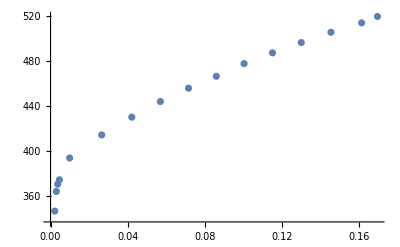

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

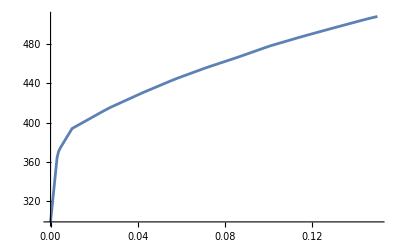

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

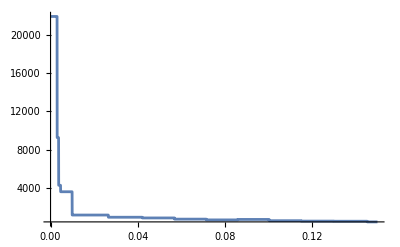

```mathematica
(*data=Import["/home/diogo/Dropbox/mathematica/modifications-bc/A500_t16_2const.csv"]*)
data=Import["/home/diogo/Dropbox/mathematica/modifications-bc/A500_t16_tensile.csv"];
data=Delete[data,1];
data2=Table[{data[[i]][[2]],data[[i]][[1]]},{i,20,Length[data]}];
data2=DeleteDuplicates[data2];
For[k=1,k<=4,k++,
For[j=1,j<Length[data2],j++,
For[i=1,i<Length[data2],i++,
If[data2[[i]][[1]]==data2[[j]][[1]],
data2=Delete[data2,i];
];
If[data2[[i]][[2]]<330,
data2=Delete[data2,i];
];
];
];
];
ListPlot[data2]
expfunc=Interpolation[data2,InterpolationOrder->1];
pl=Plot[expfunc[x],{x,0,0.15},PlotRange->All]
deriv=D[expfunc[x],x];
Plot[expfunc'[x],{x,0,0.15},PlotRange->All]
sigyfunc[eps_]:=Block[{},
{expfunc[eps],expfunc'[eps]}
];
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

200000.

100000.

66666.7

{298.475,100000.,66666.7}

{0.,0,0,0,0,0}

500

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{66666.7,66666.7,66666.7,0.,0.,0.},{66666.7,160387.,-27053.4,0.,0.,0.},{66666.7,-27053.4,160387.,0.,0.,0.},{0.,0.,0.,93720.1,0.,0.},{0.,0.,0.,0.,93720.1,0.},{0.,0.,0.,0.,0.,93720.1}}

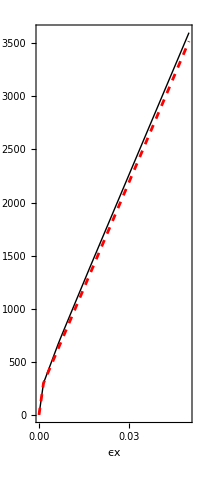

```mathematica
flag=1;
young=200000;
nu=0.0;
sigy=sigyfunc[0][[1]];
epspintold=0;
epspintold2=0;
c=young (1-nu)/((1+nu)(1-2nu))
G=young/(2(1+nu))
K=young/(3(1-2nu))
subst2={sigy,young/(2(1+nu)),(young)/(3 (1-2nu))}
epst={0.,0,0,0,0,0}
epsp={0,0,0,0,0,0};
epst2=epst;
epsp2=epsp;
hard=0.;
epsvec={};
sigvec={};
epsvec2={};
sigvec2={};
steps=500;
loadsize=500
deps={0.0001,0,0,0,0,0.000};
For[i=1,i<steps,i++,
{stress,Dep,cmat}=ApplyStrainComputeSigmaDepVonMisesCPP[epst,epsp,subst2];
(*{stress,Dep,cmat,epspbar}=ApplyStrainComputeSigmaDepVonMises[epst,epsp,epspintold,subst2];*)
(*{stress,Dep,cmat}=ApplyStrainComputeSigmaDepVonMisesCPP[epst,epsp,subst2];*)
{stress2,Dep2,cmat2,epspbar2}=ApplyStrainComputeSigmaDepVonMisesIsoHard[epst2,epsp2,epspintold2,subst2];
epspintold2=epspbar2;
eps2=Inverse[cmat2].stress2;
epsp2=epst2-eps2;
epspintold=epspbar;
eps=Inverse[cmat].stress;
(*hard+=hard0;*)
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[epsvec2,epst2];
AppendTo[sigvec2,stress2];
(*If[ Mod[i,loadsize]==0,
deps*=-1;
];*)
(*If[ i==100,
deps*=-1;
];*)
epst+=deps;
epst2+=deps;
];
Dep
solpsx=Table[epsvec[[i,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1]],{i,1,Length[sigvec]}];
plot2=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"},AspectRatio->Full,PlotStyle->{Red,Dashed}];

solpsx2=Table[epsvec2[[i,1]],{i,1,Length[epsvec2]}];
solsigx2=Table[sigvec2[[i,1]],{i,1,Length[sigvec2]}];
plot22=ListLinePlot[Table[Tooltip[{solpsx2[[i]],solsigx2[[i]]}],{i,1,Length[solpsx2]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"},AspectRatio->Full,PlotStyle->{Black,Thick}];
Show[plot22,plot2]
```

```mathematica
Dep//MatrixForm
```

Dep

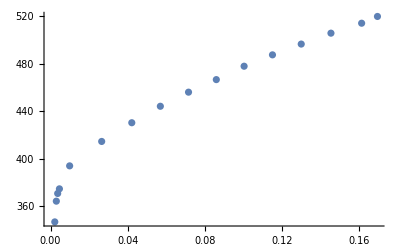

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

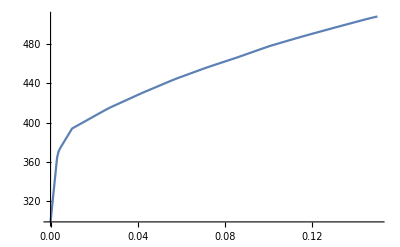

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

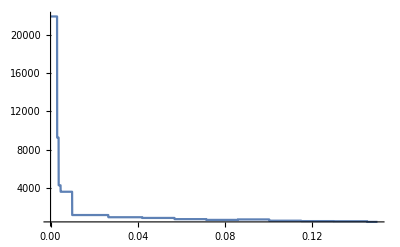

```mathematica
(*data=Import["/home/diogo/Dropbox/mathematica/modifications-bc/A500_t16_2const.csv"]*)
data=Import["/home/diogo/Dropbox/mathematica/modifications-bc/A500_t16_tensile.csv"];
data=Delete[data,1];
data2=Table[{data[[i]][[2]],data[[i]][[1]]},{i,20,Length[data]}];
data2=DeleteDuplicates[data2];
For[k=1,k<=4,k++,
For[j=1,j<Length[data2],j++,
For[i=1,i<Length[data2],i++,
If[data2[[i]][[1]]==data2[[j]][[1]],
data2=Delete[data2,i];
];
If[data2[[i]][[2]]<330,
data2=Delete[data2,i];
];
];
];
];
ListPlot[data2]
expfunc=Interpolation[data2,InterpolationOrder->1];
pl=Plot[expfunc[x],{x,0,0.15},PlotRange->All]
deriv=D[expfunc[x],x];
Plot[expfunc'[x],{x,0,0.15},PlotRange->All]
sigyfunc[eps_]:=Block[{},
{expfunc[eps],expfunc'[eps]}
];
(*sigyfunc[eps_]:=Block[{hardeningmod=10000,yieldstress=200},
{yieldstress + hardeningmod eps  ,  hardeningmod   }
];*)
```

```mathematica
data2
```

{{0.0022,346.6},{0.003,364.1},{0.0037,370.6},{0.0046,374.5},{0.0099,393.9},{0.0265,414.5},{0.0421,430.3},{0.0569,444.2},{0.0715,456.1},{0.0859,466.7},{0.1003,478.},{0.115,487.6},{0.1299,496.7},{0.1453,505.9},{0.1612,514.3},{0.1694,520.}}

```mathematica
epbarn=0.;

flag=1;
young=210000;
nu=0.0;
sigy=0;
c=young (1-nu)/((1+nu)(1-2nu))
G=young/(2(1+nu))
K=young/(3(1-2nu))
subst2={sigy,young/(2(1+nu)),(young)/(3 (1-2nu))}
epst={0.,0,0,0,0,0}
epsp={0,0,0,0,0,0};
epspintold=0;
hard=0.;
epsvec={};
sigvec={};
steps=50;
loadsize=50
deps={0.0001,0,0,0,0,0};
For[i=1,i<steps,i++,
(*Print["pspt = ",epst];
Print["epsp = ",epsp];*)
{stress,Dep,cmat,epspbar}=ApplyStrainComputeSigmaDepVonMisesIsoHard[epst,epsp,epspintold,subst2];
epspintold=epspbar;
eps=Inverse[cmat].stress;
(*hard+=hard0;*)
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
epst+=deps;
];
Dep
solpsx=Table[epsvec[[i,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1]],{i,1,Length[sigvec]}];
plot2=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"},AspectRatio->Full,PlotMarkers->{Automatic, 10}]
(556.194-341.589)/(0.00339595-0.00155648)
solpsx=Table[epsvec[[i,1]],{i,1,Length[epsvec]}];
solsigxy=Table[sigvec[[i,6]],{i,1,Length[sigvec]}];
plot2=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigxy[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σxy"},AspectRatio->Full,PlotMarkers->{Automatic, 10}]
(-29.6404-33.3596)/(0.00311296-0.000565992)
```

210000.

105000.

70000.

{0,105000.,70000.}

{0.,0,0,0,0,0}

50

rhotrial = 0.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

rhoproj = 243.704

Inverse::mindet: Input matrix contains an indeterminate entry.

Inverse[{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}].{{210000.,0.,0.,0,0,0},{0.,210000.,0.,0,0,0},{0.,0.,210000.,0,0,0},{0,0,0,105000.,0,0},{0,0,0,0,105000.,0},{0,0,0,0,0,105000.}}-Inverse[{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}]^2.{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}.Indeterminate/{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}.Inverse[{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}].{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

Part::partd: Part specification {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth}⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth}⟦3,1⟧ is longer than depth of object.

Part::partd: Part specification {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth}⟦4,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

116667.

Part::partd: Part specification {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth}⟦2,6⟧ is longer than depth of object.

Part::partd: Part specification {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth}⟦3,6⟧ is longer than depth of object.

Part::partd: Part specification {{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth,sigprojvoigth}⟦4,6⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

-24735.3

```mathematica
0.05/0.0001
```

500.

```mathematica
epbarn
```

0.

```mathematica
Norm[epsp]
```

0.00548695